## Sample generation :

```mathematica
(* 0 Define variables*)
SetDirectory[NotebookDirectory[]];
$HistoryLength = 0;

numPoint=1000; cl=0.01; 
nameSample="Sample"<>ToString[numPoint];
nameMass="Mass"<>ToString[numPoint];

N1=5;ps=0.0;
vari=Table[Subscript[x,n],{n,0,N1-1}];
variC=Table[Subscript[OverBar[x],n],{n,0,N1-1}];
complexConjugate=Join[Thread[vari->variC],Thread[variC->vari]];
DefPoly=Total[vari^(N1)]-ps*N1*Times@@vari;
 npA=Length[vari]-1;npX=npA-1; nCor=Length[vari]; dimP=npX;
Print[DefPoly];

(* patch information *)
tuples=vari;
patches = Table[{vari[[i]]-> 1}, {i, 1, Length[vari]}];
nP=Length[patches];gnumPoint=nP*numPoint;

(* redundent coordinate information *)
redunC={1,1,1,1,1};
inhomoCors=Table[RotateRight[Delete[vari, pth],npA-redunC[[pth]]],{pth,1,Length[tuples]}];
complexConjugate=Thread[vari->variC];
CinhomoCors=inhomoCors/.complexConjugate;
Print["The redundent coordinates on every patch are "<>ToString[redunC]];
```

0.+x_0^5+x_1^5+x_2^5+x_3^5+x_4^5

The redundent coordinates on every patch are {1, 1, 1, 1, 1}

Generate points in Disk before intersection  1000

We generate global points with number {5990, 5}

We generate sample with number {5, 1000, 5}

We get sample points {5, 1000, 5}

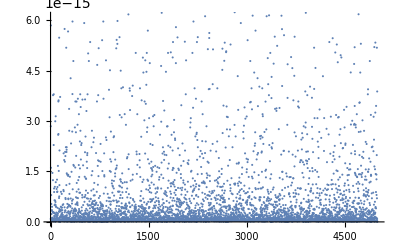

```mathematica
(* generate the uniformly distributed points on the n-sphere (norm distribution) *)
normS[m_]:=m/Norm[m];
complexifyP[m_]:=Complex@@@Partition[m,2];
ptS=complexifyP/@normS/@Transpose[Table[RandomVariate[NormalDistribution[0,1],numPoint],{i,1,nCor*2}]];
Print["Generate points in Disk before intersection  "<>ToString[Length[ptS]]];

(* generate the intersection points on the calabi-yau manifold *)
interCY[m_]:=Module[{tpoint,tDefpoly,t},tpoint=m[[1]]+t*m[[2]];
tDefpoly=DefPoly/.Thread[vari->tpoint];
tpoint/.Solve[tDefpoly==0,t]];
smallQ[m_]:=Min[Abs[m]]>cl;
gCYpts=Select[Flatten[Table[interCY[RandomChoice[ptS,2]],{i,1,Floor[gnumPoint/Length[tuples]*1.2]}],1],smallQ];
Print["We generate global points with number "<>ToString[Dimensions[gCYpts]]];

(* reform the data and make sure that every patch has the same number of data *)
pathCors[m_List]:=Module[{tm},tm=Abs[m];Position[tm,Max[tm]]];
inx=Flatten[pathCors/@gCYpts];
(*numPoint=Min[Table[Count[inx,i],{i,1,4}]];*)
lCYpts=Table[Pick[gCYpts,inx,i][[1;;numPoint]],{i,1,Length[tuples]}];
Print["We generate sample with number "<>ToString[Dimensions[lCYpts]]];
Print["We get sample points " <> ToString[Dimensions[lCYpts]]];
(*Export[ nameSample,Flatten[lCYpts,1], {"Binary", "Complex128"}];
Share[];*)

(*Check the accuracy of sample using global points*)
TestCYSample[ptCY_List]:=Abs[DefPoly/.Thread[vari->ptCY]];
Print[ListPlot[TestCYSample/@Flatten[lCYpts,1]]];
```

#### B. Project global points to local points on patches and compute the mass

We get sample points {5, 1000, 4}

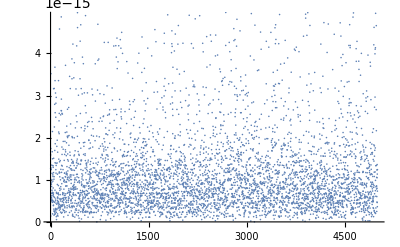

```mathematica
glob2loc[CYpoints_,redunC_]:=Module[{pth,tCYpointsl,tm,shift},
For[pth=1;tCYpointsl={},pth≤Length[tuples],pth++,
tm=CYpoints[[pth]];shift=npA-redunC[[pth]];
tCYpointsl=AppendTo[tCYpointsl,Table[RotateRight[Delete[tm[[pt]]/tm[[pt,pth]],pth],shift],{pt,1,numPoint,1}]];];
tCYpointsl
];
CYpointsl=glob2loc[lCYpts,redunC];
Print["We get sample points " <> ToString[Dimensions[CYpointsl]]];
Export[ nameSample,Flatten[CYpointsl,1], {"Binary", "Complex128"}];

(*Check the accuracy of sample using local points*)
TestCYSampleLoc[ptCY_List,pth_Integer]:=Module[{rep},
rep=Join[{vari[[pth]]->1},Thread[inhomoCors[[pth]]->ptCY]];
Abs[DefPoly/.rep]];

errs=Table[TestCYSampleLoc[CYpointsl[[pth,pt]],pth],{pth,1,Length[tuples]},{pt,1,numPoint}];
Print[ListPlot[Flatten[errs]]];
```

#### C. Mass for points on each patch:

```mathematica
gA2X[JA_,Qa_]:=Module[{tQa},
tQa=Delete[Qa/Qa[[npA]],npA];
Table[JA[[i,j]]-JA[[i,npA]]*Conjugate[tQa[[j]]]-tQa[[i]]*JA[[npA,j]]+tQa[[i]]*JA[[npA,npA]]*Conjugate[tQa[[j]]],{i,1,npX},{j,1,npX}]];

getMass[JA_,Qa_]:=N[1.0/(Det[gA2X[JA,Qa]]*Abs[Qa[[npA]]]^2)];

massG[CYpointsl_]:=Module[{K,pth,Kl,DefPolyl,JAab,Qa,HICComplex,conj,JAfunc,Qafunc,tmass,point}, 

(* Kahler potential for FS metric *)
K=Log[Total[vari*variC]];

For[pth=1;tmass={},pth≤Length[tuples],pth++,

Kl=K/.{vari[[pth]]->1,variC[[pth]]->1};
JAab=D[D[Kl,{inhomoCors[[pth]]}],{CinhomoCors[[pth]]}];
DefPolyl=DefPoly/.{vari[[pth]]->1};
Qa=D[DefPolyl,{inhomoCors[[pth]]}];

HICComplex = ( {#, _Complex} & ) /@ inhomoCors[[pth]];
conj = Thread[ CinhomoCors[[pth]] -> Conjugate[inhomoCors[[pth]] ] ];
JAfunc = Compile[Evaluate[ HICComplex ], Evaluate[ToExpression[ ToString[JAab/.conj, StandardForm]]]];
Qafunc= Compile[Evaluate[ HICComplex ], Evaluate[ToExpression[ ToString[Qa/.conj, StandardForm]]]];

tmass =AppendTo[tmass,Re[ParallelTable[point=CYpointsl[[pth,pt]];
getMass[JAfunc@@point,Qafunc@@point],{pt,1,numPoint,1}]]];
];
tmass
];
mass=massG[CYpointsl]/N[gnumPoint];
volCY=Total[Flatten[mass]];
Print[{"The volumn of X is ",volCY}];
Export[ nameMass,Flatten[mass,1], {"Binary", "Real128"}];
```

{The volumn of X is ,1.84484}

## Donaldson' s algorithm :

```mathematica
SetDirectory[NotebookDirectory[]];
(*0 Define variables*)
$HistoryLength=0;

Hth=1;nIter=60;
nameH="HBK"<>ToString[k]<>"_"; 
nameHH="HBK2_100";


N1=5;
vari=Table[Subscript[x,n],{n,0,N1-1}];
variC=Table[Subscript[OverBar[x],n],{n,0,N1-1}];
npA=N1-1;npX=npA-1;nP=Length[vari]-1;
ps=0.0;
DefPoly=Total[vari^N1]-N1 ps Times@@vari;
Print[DefPoly];

(* patch information *)
patches = Table[{vari[[i]]-> 1}, {i, 1, Length[vari]}];
(* redundent coordinate information *)
redunC=ConstantArray[1,{Length[vari]}];
inhomoCors=Table[RotateRight[Delete[vari, pth],npA-redunC[[pth]]],{pth,1,Length[patches]}];
complexConjugate=Thread[vari->variC];
CinhomoCors=inhomoCors/.complexConjugate;
Print["The redundent coordinates on every patch are "<>ToString[redunC]];

(* possible symmetries *)
findInvZ5[monos_]:=Module[{index},
DeleteCases[Table[If[monos[[i]]-(monos[[i]]/.rep2)===0,monos[[i]],0],{i,1,Length[monos]}],0]
];

findRep[element_,basis_List]:=Module[{vari,as,genSec,tt},
vari=Variables[basis];
as=Table[Subscript[a, i],{i,1,Length[basis]}];
genSec=as.basis;
tt=DeleteCases[Flatten[CoefficientList[element-genSec,vari]],0];
Solve[Table[tt[[i]]==0,{i,1,Length[tt]}],as][[1]]/.Rule->(#2&)
];
α=Exp[I 2 Pi/5];
rep1={Subscript[x, 0]->Subscript[x, 1],Subscript[x, 1]->Subscript[x, 2],Subscript[x, 2]->Subscript[x, 3],Subscript[x, 3]->Subscript[x, 4],Subscript[x, 4]->Subscript[x, 0]};
rep2={Subscript[x, 0]->Subscript[x, 0],Subscript[x, 1]->α Subscript[x, 1],Subscript[x, 2]->α^2 Subscript[x, 2],Subscript[x, 3]->α^3 Subscript[x, 3],Subscript[x, 4]->α^4 Subscript[x, 4]};
tvari1=vari/.rep1;tvari2=vari/.rep2;
sym1=Table[findRep[tvari1[[i]],vari],{i,1,Length[tvari1]}];
sym2=Table[findRep[tvari2[[i]],vari],{i,1,Length[tvari2]}];
Print[MatrixForm[sym1]];
Print[MatrixForm[sym2]];
```

0.+x_0^5+x_1^5+x_2^5+x_3^5+x_4^5

The redundent coordinates on every patch are {1, 1, 1, 1, 1}

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0)

(1 | 0 | 0 | 0 | 0
0 | (-1)^(2/5) | 0 | 0 | 0
0 | 0 | (-1)^(4/5) | 0 | 0
0 | 0 | 0 | -(-1)^(1/5) | 0
0 | 0 | 0 | 0 | -(-1)^(3/5))

#### Bundle Frame :

```mathematica
k=2;rank=3; numF=4; 
tA=-4;tB1=-1;
Print[{"The bundle A is ",{tA}}];
Print[{"The bundle B is ",{tB1,tB1,tB1,tB1}}];
ktA=tA+k; ktB1=tB1+k;
Print[{"The twisted bundle A is ",{ktA}}];
Print[{"The twisted bundle B is ",{ktB1,ktB1,ktB1,ktB1}}];
indV=((4*ktB1^3-ktA^3)+5*(4*ktB1-ktA))/6;
Print[{"Index of quotinet bundle: ",indV}];

(* dim of H^0(X,L) *)
dimH0[k_]:=Module[{},
If[k==0,Return[1,Module]];
If[k>0,5*k^3/6+25*k/6,0]
];

MonoList[vari_List,Pnum_Integer]:=Module[{tp,mono,coefmono,pt,outp},pt=Abs[Pnum];tp=(Total[vari])^pt;
mono=MonomialList[tp];
coefmono=mono/.Thread[vari->Table[1,{i,1,Length[vari]}]];
outp=mono/coefmono;
If[Pnum≥0,outp,{}]];

monos=MonoList[vari,3];
index=Flatten[Position[(monos-(monos/.rep2))/.Thread[vari->{1,1,1,1,1}],0]];
invMonos=Table[monos[[index[[i]]]],{i,1,Length[index]}];

(* Need to check the bundleness *)
tBmaps=Table[RandomInteger[{-5,10},{Length[invMonos]}],{j,1,numF}];
tBmaps={{-1,-3,4,-3,-5,-3,-2},{9,8,6,3,-2,10,-1},{1,-3,-4,4,0,4,0},{-2,3,10,-2,6,1,5}}; 
bundleMap=Table[tBmaps[[i]].invMonos,{i,1,numF}];

(* The frame information *)
tframe={Subscript[e, 1],Subscript[e, 2],Subscript[e, 3],Subscript[e, 4]};
subframe=Thread[tframe->IdentityMatrix[numF]];

redunF=4; 
indframe=Complement[{1,2,3,4},{redunF}];
Print[{"The redun frame is ",redunF}];
dels = Table[bundleMap[[indframe[[i]]]]/bundleMap[[redunF]],{i,1,Length[indframe]}];
```

{The bundle A is ,{-4}}

{The bundle B is ,{-1,-1,-1,-1}}

{The twisted bundle A is ,{-2}}

{The twisted bundle B is ,{1,1,1,1}}

{Index of quotinet bundle: ,7}

{The redun frame is ,4}

```mathematica
CoeffFromMonos[m_List,monos_List]:=Module[{tcoflist,ttm,i,j,zeroB},zeroB={};
For[j=1,j≤Length[m],j++,tcoflist={};
For[i=1,i≤Length[monos],i++,ttm=Coefficient[m[[j]],monos[[i]]];
AppendTo[tcoflist,ttm]];
AppendTo[zeroB,tcoflist];];
Return[zeroB]];

H0Xs2[k_Integer,Monos_,cs_]:=Module[{Mt,Mt2,tk,tMonos,zeros,zeroBasis,q,qBasis},
If[k<5,Return[Monos];];tk=k-5;
tMonos=MonoList[vari,tk];
zeros=cs*tMonos;
zeroBasis=CoeffFromMonos[zeros,Monos];
qBasis=Dot@@{NullSpace[zeroBasis],Monos}];

(* 1 invariant basis of C on X *)
monoA=findInvZ5[MonoList[vari,ktA]]; 
monoXA= H0Xs2[ktA,monoA,DefPoly];
Print["The dim of A on CY is "<>ToString[(Length[monoXA])]];
(* 1 invariant basis of B on A *)
monoAB=Flatten[Outer[Times,findInvZ5[MonoList[vari,ktB1]], tframe]];
Print["The dim of B on A is "<>ToString[Length[monoAB]]];

(* 2 find things that need to be quotiented *)
qcs=If[ktB1<5,{},DefPoly*findInvZ5[MonoList[vari,ktB1-5]]];
quotientCS=Flatten[Outer[Times,qcs, tframe]];
quotientMap=Flatten[Table[(bundleMap*monoXA[[i]]).tframe,{i,1,Length[monoXA]}],1];
quotientPoly=Join[quotientCS,quotientMap];
Print["The dim of quotient polynomial is "<>ToString[Length[quotientCS]]<>" + "<>ToString[Length[quotientMap]]<>" = "<>ToString[Length[quotientPoly]]];

(* 3 do the quotient *)
getImageCoff[poly_]:=Table[Coefficient[poly,monoAB[[i]]],{i,1,Length[monoAB],1}];
zerosB=getImageCoff/@quotientPoly;
quotientBasis=If[Length[quotientPoly]==0,IdentityMatrix[Length[monoAB]],NullSpace[zerosB]];
qh0=Length[quotientBasis];
Print["The dim of global section on CY is "<>ToString[Length[quotientBasis]]];
qgs=Dot@@{quotientBasis,monoAB};
```

The dim of A on CY is 0

The dim of B on A is 12

The dim of quotient polynomial is 0 + 0 = 0

The dim of global section on CY is 12

#### Prepare numerical data :

```mathematica
HICComplex=Table[{#, _Complex} & /@ inhomoCors[[pth]],{pth,1,Length[patches]}];

(* Find the CF of Q *)
getfuncQa[pth_Integer]:=Module[{DefPolyl,Qa},
DefPolyl=DefPoly/.patches[[pth]];
Qa=D[DefPolyl,{inhomoCors[[pth]]}];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[Qa]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)
]];
funcQa=Table[getfuncQa[pth],{pth,1,Length[patches],1}];

(* Find the CF of Del *)
getfuncDel[pth_Integer]:=Module[{DefPolyl,delsl},
delsl = dels/.patches[[pth]];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[delsl]]];
funcDel=Table[getfuncDel[pth],{pth,1,Length[patches]}];

(* Find the CF of DDel *)
(* index structure
1st (# of frame)
2rd (# of derivative)
*)
genfuncDDel[pth_Integer]:=Module[{delsl,Ddelsl},
delsl = dels/.patches[[pth]];
Ddelsl=D[delsl, {inhomoCors[[pth]]}];
Compile[Evaluate[HICComplex[[pth]]], 
Evaluate[Ddelsl]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)]
];
funcDDel=Table[genfuncDDel[pth],{pth,1,Length[patches]}];

(* Find the CF of s *)
getfuncSb[pth_Integer]:=Module[{DefPolyl,qBasisl},
qBasisl = monoAB/.subframe/.patches[[pth]];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[qBasisl]]];
funcSb=Table[getfuncSb[pth],{pth,1,Length[patches]}];

(* Find the CF of ds *)
(* index structure
1st  (# of section)
2rd  (# of frame)
3rd  (# of derivative)
*)
genfuncSbd[pth_Integer]:=Module[{qBasisl,dqBasisl},
qBasisl = monoAB/.subframe/.patches[[pth]];
dqBasisl=D[qBasisl, {inhomoCors[[pth]]}];
Compile[Evaluate[HICComplex[[pth]]], 
Evaluate[dqBasisl]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)]
];
funcSbd=Table[genfuncSbd[pth],{pth,1,Length[patches]}];
```

#### Read the data :

```mathematica
(*2 Read the data from files *)
getPointsFile[filename_String] := Module[{stream},
           stream = OpenRead[ filename, BinaryFormat -> True ];
          Partition[
                 BinaryReadList[ stream, "Complex128" ], npA]
           ];
getPointsFile2[filename_String] := Module[{stream},
           stream = OpenRead[ filename, BinaryFormat -> True ];
      BinaryReadList[ stream, "Real128" ]
           ];

numPoint=1000;
nameS="Sample1000";
nameW="Mass1000";

CYpoints=getPointsFile[nameS];gnumPoint=Length[CYpoints];
massCY =Re[ getPointsFile2[nameW]]/N[gnumPoint];
Print["2a) We get sample "<>ToString[gnumPoint]];

volCY=Total[massCY]; 
Print[{"The volumn is ",volCY}];

indexData[numCY_List,numpp_Integer]:=Module[{tcount},tcount=0;
Join[{0},Table[tcount+=numCY[[pth]],{pth,1,numpp-1,1}]]];
numCY = ConstantArray[numPoint,Length[patches]];
count=indexData[numCY,Length[patches]];

getH[filename_String] := Module[{stream},
         stream = OpenRead[ filename, BinaryFormat -> True ];
   Partition[BinaryReadList[ stream, "Complex128" ], qh0]
        ];
Hp0 = If[Hth == 1, IdentityMatrix[qh0], getH[nameHH]];
Print[{"This is ", Hth, " times interation for H"}];
```

2a) We get sample 5000

{The volumn is ,1.83354}

{This is ,1, times interation for H}

#### T - operator :

```mathematica
getT[s_, H_] := Module[{cs,InG,T},
cs=Conjugate[s];
(*InG=Check[Inverse[Transpose[cs].H.s],Print["error "<>ToString[pt]]];*)
(*Print[Transpose[cs].H.s];*)
InG=Inverse[Transpose[cs].H.s];
(*Print[InG];*)
T=s.InG.Transpose[cs]];

Toperator[] := Module[{pth,  pt,T,constrP,subConstr,PqGS, Sfunc,nRedun,varil,HICComplex,tpoint,point},

ParallelEvaluate[tT=ConstantArray[0.,{qh0,qh0}];];

lnH=Inverse[H];DistributeDefinitions[lnH];
Table[DistributeDefinitions[pth];

	ParallelTable[ 

point=CYpoints[[pt]];  
Delpt=funcDel[[pth]]@@point; 
Spt1=Transpose[quotientBasis.funcSb[[pth]]@@point];
Spt=Transpose[Table[Spt1[[indframe[[i]]]] - Delpt[[i]]*Spt1[[redunF]],{i,1,npX}]];
tT+=getT[Spt,lnH]*massCY[[pt]];
		,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
		Method->"CoarsestGrained",DistributedContexts->None];

	,{pth,1,Length[patches]}];
	N[qh0*Total[ParallelEvaluate[tT]]/volCY/rank]
];

Print["comm_shared_data"];time=SessionTime[];
DistributeDefinitions[CYpoints,massCY,funcQa,funcDel,funcDDel,funcSb,funcSbd,getT,npX,npA,indframe,redunF,quotientBasis,qh0];
Print[{"comm_data_done!",N[SessionTime[]-time]}];

eigenQ2[h1_,h2_] := Module[{e1,e2},
e1=Max[Abs[Eigenvalues[h1]]];
e2=Max[Abs[Eigenvalues[h2]]];
{e1,e2,Abs[(e1/e2)-1.0]}];


For[st =Hth;H = Hp0, st <= nIter, st++,
timeM = SessionTime[];

tH = Toperator[]; 
errT = eigenQ2[tH, H];H=tH;
Print[{st, errT, ToString[MaxMemoryUsed[]*1024.^-3],N[SessionTime[] - timeM]}];

If[Mod[st,20]==0,
Export[nameH<>ToString[st], H , {"Binary", "Complex128"}]];
];

(* Test the hermitian property *)
Print[Total[Flatten[H-Transpose[Conjugate[H]]]]];
```

comm_shared_data

{comm_data_done!,0.089696}

{1,{1.47392,1,0.473921},0.144371,0.336583}

{2,{1.93509,1.47392,0.312889},0.144371,0.370682}

{3,{2.4193,1.93509,0.250225},0.144371,0.417442}

{4,{2.93,2.4193,0.211093},0.144371,0.357987}

{5,{3.4512,2.93,0.177884},0.144371,0.330859}

{6,{3.95997,3.4512,0.147418},0.144371,0.341697}

{7,{4.43448,3.95997,0.119826},0.144371,0.402209}

{8,{4.85873,4.43448,0.0956724},0.144371,0.352504}

{9,{5.22431,4.85873,0.0752402},0.144371,0.333612}

{10,{5.5297,5.22431,0.0584556},0.144371,0.328011}

{11,{5.77847,5.5297,0.044988},0.144371,0.333193}

{12,{5.97711,5.77847,0.034377},0.144371,0.429235}

{13,{6.1333,5.97711,0.0261308},0.144371,0.349366}

{14,{6.25466,6.1333,0.0197875},0.144371,0.340172}

{15,{6.34813,6.25466,0.0149442},0.144371,0.356175}

{16,{6.41965,6.34813,0.011266},0.144371,0.356242}

{17,{6.47411,6.41965,0.00848318},0.144371,0.362014}

{18,{6.51544,6.47411,0.00638331},0.144371,0.328666}

{19,{6.54672,6.51544,0.00480159},0.144371,0.334048}

{20,{6.57036,6.54672,0.00361153},0.144371,0.371652}

{21,{6.58821,6.57036,0.00271673},0.144371,0.334973}

{22,{6.60168,6.58821,0.00204416},0.144371,0.332333}

{23,{6.61184,6.60168,0.00153867},0.144371,0.362642}

{24,{6.6195,6.61184,0.00115869},0.144371,0.343799}

{25,{6.62528,6.6195,0.000872984},0.144371,0.32627}

{26,{6.62964,6.62528,0.000658086},0.144371,0.614592}

{27,{6.63293,6.62964,0.000496374},0.144371,0.482157}

{28,{6.63542,6.63293,0.000374623},0.144371,0.461479}

{29,{6.63729,6.63542,0.000282908},0.144371,0.461621}

{30,{6.63871,6.63729,0.000213779},0.144371,0.521617}

{31,{6.63978,6.63871,0.000161642},0.144371,0.388623}

{32,{6.6406,6.63978,0.000122297},0.144371,0.391575}

{33,{6.64121,6.6406,0.0000925871},0.144371,0.473798}

{34,{6.64168,6.64121,0.000070138},0.144371,0.421631}

{35,{6.64203,6.64168,0.0000531647},0.144371,0.355215}

{36,{6.6423,6.64203,0.0000403235},0.144371,0.313687}

{37,{6.6425,6.6423,0.0000306024},0.144371,0.322487}

{38,{6.64266,6.6425,0.0000232386},0.144371,0.313594}

{39,{6.64277,6.64266,0.0000176571},0.144371,0.549903}

{40,{6.64286,6.64277,0.0000134238},0.144371,0.432685}

{41,{6.64293,6.64286,0.0000102113},0.144371,0.342046}

{42,{6.64298,6.64293,7.77186×10^-6},0.144371,0.319825}

{43,{6.64302,6.64298,5.91842×10^-6},0.144371,0.34049}

{44,{6.64305,6.64302,4.50939×10^-6},0.144371,0.406564}

{45,{6.64307,6.64305,3.4376×10^-6},0.144371,0.392635}

{46,{6.64309,6.64307,2.62189×10^-6},0.144371,0.423348}

{47,{6.6431,6.64309,2.00074×10^-6},0.144371,0.352585}

{48,{6.64311,6.6431,1.52749×10^-6},0.144371,0.324735}

{49,{6.64312,6.64311,1.16673×10^-6},0.144371,0.332134}

{50,{6.64313,6.64312,8.91591×10^-7},0.144371,0.406308}

{51,{6.64313,6.64313,6.81642×10^-7},0.144371,0.463724}

{52,{6.64314,6.64313,5.2136×10^-7},0.144371,0.523332}

{53,{6.64314,6.64314,3.98938×10^-7},0.144371,0.322659}

{54,{6.64314,6.64314,3.05389×10^-7},0.144371,0.330501}

{55,{6.64314,6.64314,2.33872×10^-7},0.144371,0.326216}

{56,{6.64314,6.64314,1.79173×10^-7},0.144371,0.373875}

{57,{6.64314,6.64314,1.37321×10^-7},0.144371,0.408033}

{58,{6.64315,6.64314,1.05283×10^-7},0.144371,0.408264}

{59,{6.64315,6.64315,8.07495×10^-8},0.144371,0.421904}

{60,{6.64315,6.64315,6.19545×10^-8},0.144371,0.383946}

0.-4.61659×10^-15 ⅈ

#### Compute the error of connection :

```mathematica
nameMetric="nmetricK5";
(* Read the metric! *)
getMetricFile[filename_String] := Module[{stream},
      stream = OpenRead[ filename, BinaryFormat -> True ];
       Partition[Partition[
            BinaryReadList[ stream, "Complex128" ], 
      npX],npX]  ];

lnNmetric=Inverse/@getMetricFile[nameMetric]; 
Print[{"The metric is ",Dimensions[lnNmetric]}];
```

{The metric is ,{5000,3,3}}

```mathematica
getV3[s_,ds_,lNmetric_,H_]:=Module[{cs,cds,i,j,ts,InG,dG,cdG,ddG,Mb,tM,M,tr,eign},
(* H: 1st is anti; 2nd is homo *)
cs=Conjugate[s];  cds=Conjugate[ds];

InG=Inverse[Transpose[cs].H.s];
dG=Table[Transpose[cs].H.ds[[a]],{a,1,npX}];
cdG=Table[Transpose[cds[[b]]].H.s,{b,1,npX}];
ddG=Sum[lNmetric[[b,a]]*Transpose[cds[[b]]].H.ds[[a]],{a,1,npX},{b,1,npX}];

Mb=Sum[lNmetric[[b,a]]*cdG[[b]].InG.dG[[a]],{a,1,npX},{b,1,npX}];
tM=InG.(ddG-Mb);
M=N[tM-Tr[tM]*IdentityMatrix[rank]/rank];
N[Total[Abs/@Eigenvalues[M]]]
];

getError[H_,TNmetric_] := Module[{pth,pt,error,point},

For[pth=1;error=0.0,pth≤Length[patches],pth++,
DistributeDefinitions[pth];Print[pth];
error+=ParallelSum[
point=CYpoints[[pt]];  
(* Find the S *)
Delpt=funcDel[[pth]]@@point; 
Spt1=Transpose[quotientBasis.funcSb[[pth]]@@point];
Spt=Transpose[Table[Spt1[[indframe[[i]]]] - Delpt[[i]]*Spt1[[redunF]],{i,1,npX}]];

(* Find the dS *)
Qpt=funcQa[[pth]]@@point; 
DDelpt=funcDDel[[pth]]@@point; 
tDSpt=Transpose[quotientBasis.funcSbd[[pth]]@@point,{3,1,2}];
DSpt1=Transpose[Table[tDSpt[[indframe[[i]],j]]-DDelpt[[indframe[[i]],j]]*Spt1[[redunF]]-tDSpt[[redunF,j]]*Delpt[[indframe[[i]]]],{i,1,3},{j,1,npA}],{2,1,3}];
DSpt=Transpose[Table[DSpt1[[i]]-(Qpt[[i]]/Qpt[[npA]])*DSpt1[[npA]],{i,1,npX,1}],{1,3,2}];

 getV3[Spt,DSpt,TNmetric[[pt]],H]*massCY[[pt]]
		,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
		Method->"CoarsestGrained",DistributedContexts->None];
Print[ParallelEvaluate[MaxMemoryUsed[]*1024.^-3]];
];
N[error]/volCY/rank
];

Print[getError[lnH,lnNmetric]];
```

1.65811

#### 5. Finish and Clean

```mathematica
Print["Wall time in the code "<>ToString[SessionTime[]]];
Print["The maximum memeory used in the code "<>ToString[MaxMemoryUsed[]*1024.^-3]];
CloseKernels[];
Exit[];
```

Wall time in the code 681.597712

The maximum memeory used in the code 0.212547

## Generalized Donaldson' s algorithm :

#### Define the manifold :

```mathematica
SetDirectory[NotebookDirectory[]];
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
(*0 Define variables*)
$HistoryLength=0;

k=5;nIter=20;

numPoint=10000;
nameS="Sample"<>ToString[numPoint];
nameW="Mass"<>ToString[numPoint];

Hth=2;
nameH="HBK"<>ToString[k]<>"_";
nameHH="HBK5_20";


N1=5;
vari=Table[Subscript[x,n],{n,0,N1-1}];
variC=Table[Subscript[OverBar[x],n],{n,0,N1-1}];
npA=N1-1;npX=npA-1;nP=Length[vari]-1;
ps=0.0;
DefPoly=Total[vari^N1]-N1 ps Times@@vari;
Print[DefPoly];

(* patch information *)
patches = Table[{vari[[i]]-> 1}, {i, 1, Length[vari]}];
(* redundent coordinate information *)
redunC=ConstantArray[1,{Length[vari]}];
inhomoCors=Table[RotateRight[Delete[vari, pth],npA-redunC[[pth]]],{pth,1,Length[patches]}];
complexConjugate=Thread[vari->variC];
CinhomoCors=inhomoCors/.complexConjugate;
Print["The redundent coordinates on every patch are "<>ToString[redunC]];

(* possible symmetries *)
findRep[element_,basis_List]:=Module[{vari,as,genSec,tt},
vari=Variables[basis];
as=Table[Subscript[a, i],{i,1,Length[basis]}];
genSec=as.basis;
tt=DeleteCases[Flatten[CoefficientList[element-genSec,vari]],0];
Solve[Table[tt[[i]]==0,{i,1,Length[tt]}],as][[1]]/.Rule->(#2&)];
α=Exp[I 2 Pi/5];
rep1={Subscript[x, 0]->Subscript[x, 1],Subscript[x, 1]->Subscript[x, 2],Subscript[x, 2]->Subscript[x, 3],Subscript[x, 3]->Subscript[x, 4],Subscript[x, 4]->Subscript[x, 0]};
rep2={Subscript[x, 0]->Subscript[x, 0],Subscript[x, 1]->α Subscript[x, 1],Subscript[x, 2]->α^2 Subscript[x, 2],Subscript[x, 3]->α^3 Subscript[x, 3],Subscript[x, 4]->α^4 Subscript[x, 4]};
tvari1=vari/.rep1;tvari2=vari/.rep2;
sym1=Table[findRep[tvari1[[i]],vari],{i,1,Length[tvari1]}];
sym2=Table[findRep[tvari2[[i]],vari],{i,1,Length[tvari2]}];
Print[MatrixForm[sym1]];
Print[MatrixForm[sym2]];
```

0.+x_0^5+x_1^5+x_2^5+x_3^5+x_4^5

The redundent coordinates on every patch are {1, 1, 1, 1, 1}

(0 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0)

(1 | 0 | 0 | 0 | 0
0 | (-1)^(2/5) | 0 | 0 | 0
0 | 0 | (-1)^(4/5) | 0 | 0
0 | 0 | 0 | -(-1)^(1/5) | 0
0 | 0 | 0 | 0 | -(-1)^(3/5))

#### Global Section :

```mathematica
MonoList[vari_List,Pnum_Integer]:=Module[{tp,mono,coefmono,pt,outp},pt=Abs[Pnum];tp=(Total[vari])^pt;
mono=MonomialList[tp];
coefmono=mono/.Thread[vari->Table[1,{i,1,Length[vari]}]];
outp=mono/coefmono;
If[Pnum≥0,outp,{}]];

CoeffFromMonos[m_List,monos_List]:=Module[{tcoflist,ttm,i,j,zeroB},zeroB={};
For[j=1,j≤Length[m],j++,tcoflist={};
For[i=1,i≤Length[monos],i++,ttm=Coefficient[m[[j]],monos[[i]]];
AppendTo[tcoflist,ttm]];
AppendTo[zeroB,tcoflist];];
Return[zeroB]];

findInvZ5[monos_]:=Module[{index},
DeleteCases[Table[If[monos[[i]]-(monos[[i]]/.rep2)===0,monos[[i]],0],{i,1,Length[monos]}],0]
];

H0Xs2[k_Integer,Monos_,cs_]:=Module[{Mt,Mt2,tk,tMonos,zeros,zeroBasis,q,qBasis},
If[k<5,Return[Monos];];tk=k-5;
tMonos=MonoList[vari,tk];
zeros=cs*tMonos;
zeroBasis=CoeffFromMonos[zeros,Monos];
qBasis=Dot@@{NullSpace[zeroBasis],Monos}];

(* 1 invariant basis of C on X *)
monos=findInvZ5[MonoList[vari,k]]; 
invqBasis= H0Xs2[k,monos,DefPoly];
qh0=Length[invqBasis];
Print["The Z5 invariant global sections have dim "<>ToString[qh0]];
indL=k^3/6+5*k/6;
Print[{"The Z5 invariant global sections from index theorem ",indL}];
```

The Z5 invariant global sections have dim 25

{The Z5 invariant global sections from index theorem ,25}

#### Prepare Numeric Data :

```mathematica
(*2 Read the data from files *)
getPointsFile[filename_String] := Module[{stream},
           stream = OpenRead[ filename, BinaryFormat -> True ];
          Partition[
                 BinaryReadList[ stream, "Complex128" ], npA]
           ];

getPointsFile2[filename_String] := Module[{stream},
           stream = OpenRead[ filename, BinaryFormat -> True ];
      BinaryReadList[ stream, "Real128" ]
           ];


CYpoints=getPointsFile[nameS];gnumPoint=Length[CYpoints];
Print["2a) We get sample "<>ToString[gnumPoint]];

massCY =Re[ getPointsFile2[nameW]]/N[gnumPoint];
volCY=Total[massCY]; 
Print[{"The volumn is ",volCY}];

indexData[numCY_List,numpp_Integer]:=Module[{tcount},tcount=0;
Join[{0},Table[tcount+=numCY[[pth]],{pth,1,numpp-1,1}]]];
numCY = ConstantArray[numPoint,Length[patches]];
count=indexData[numCY,Length[patches]];



getH[filename_String] := Module[{stream},
         stream = OpenRead[ filename, BinaryFormat -> True ];
   Partition[BinaryReadList[ stream, "Complex128" ], qh0]
        ];
Hp0 = If[Hth == 1, IdentityMatrix[qh0], getH[nameHH]];
Print[{"This is ", Hth, " times interation for H"}];
```

2a) We get sample 50000

{The volumn is ,1.83499}

{This is ,2, times interation for H}

```mathematica
errCYpoints=Sum[
lDef=DefPoly/.patches[[pth]];
Sum[lDef/.Thread[inhomoCors[[pth]]->CYpoints[[pt]]],{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1}],
{pth,1,Length[vari]}];
Print[errCYpoints];
```

-7.92283×10^-13+1.16507×10^-12 ⅈ

```mathematica
HICComplex=Table[{#, _Complex} & /@ inhomoCors[[pth]],{pth,1,Length[patches]}];
(* Find the CF of Q *)
getfuncQa[pth_Integer]:=Module[{DefPolyl,Qa},
DefPolyl=DefPoly/.patches[[pth]];
Qa=D[DefPolyl,{inhomoCors[[pth]]}];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[Qa]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)
]];
funcQa=Table[getfuncQa[pth],{pth,1,Length[patches],1}];

(* Find the CF of s *)
getfuncS[pth_Integer]:=Module[{DefPolyl,qBasisl},
qBasisl = invqBasis/.patches[[pth]];
Compile[Evaluate[ HICComplex[[pth]] ], Evaluate[qBasisl]]];
funcS=Table[getfuncS[pth],{pth,1,Length[patches]}];

(* Find the CF of ds *)
genfuncSd[pth_Integer]:=Module[{qBasisl,dqBasisl},
qBasisl = invqBasis/.patches[[pth]];
dqBasisl=D[qBasisl, {inhomoCors[[pth]]}];
Compile[Evaluate[HICComplex[[pth]]], 
Evaluate[dqBasisl]
(*,CompilationTarget->"C",RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)]
];
funcSd=Table[genfuncSd[pth],{pth,1,Length[patches]}];
```

#### T - operator:

```mathematica
getT2=Compile[{{s,_Complex,1},{H,_Complex,2}}, Module[{cs,InG,qh0,iP},
qh0=Length[s];
cs=Conjugate[s];
iP =cs.H.s;
Table[s[[A1]]*cs[[B1]], {A1, 1, qh0}, {B1, 1, qh0}]/iP
]
(*,CompilationTarget->"C"
,RuntimeOptions->"Speed",RuntimeAttributes->Listable,Parallelization->True*)];

Print["comm_shared_data"];time=SessionTime[];
DistributeDefinitions[CYpoints,massCY,funcS,getT2,qh0];
Print[{"comm_data_done!",N[SessionTime[]-time]}];

Toperator[] := Module[{},
	ParallelEvaluate[tT=ConstantArray[0.,{qh0,qh0}];];
	lnH=Inverse[H];DistributeDefinitions[lnH];
	Table[
	DistributeDefinitions[pth];
	ParallelTable[
		point=CYpoints[[pt]];
		tT+=getT2[funcS[[pth]]@@point,lnH]*massCY[[pt]];
	,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
	Method->"CoarsestGrained",DistributedContexts->None];
,{pth,1,Length[patches]}];
N[qh0*Total[ParallelEvaluate[tT]]/volCY]
];

eigenQ2[h1_,h2_] := Module[{e1,e2},
	e1=Max[Abs[Eigenvalues[h1]]];
	e2=Max[Abs[Eigenvalues[h2]]];
	Abs[(e1/e2)-1.0]];

Hp0=IdentityMatrix[qh0];
For[st =Hth;H = Hp0, st <= 10, st++,
	timeM = SessionTime[];
	tH = Toperator[]; 
	errT = eigenQ2[tH, H];H=tH;
	Print[{st, errT, N[SessionTime[] - timeM]}];
	If[Mod[st,20]==0,Export[ nameH<>ToString[st], H , {"Binary", "Complex128"}]];
];
```

comm_shared_data

{comm_data_done!,0.004704}

{2,6.02703,2.04274}

{3,0.484625,1.82368}

{4,0.0836429,1.93349}

{5,0.0212402,1.90854}

{6,0.0060635,1.63623}

{7,0.00177796,1.96386}

{8,0.00052435,1.82802}

{9,0.000154843,1.63583}

{10,0.0000457428,1.81567}

```mathematica
nameMetric="nmetricK"<>ToString[k];

Print["comm_shared_data"];time=SessionTime[];
DistributeDefinitions[funcQa,funcSd,gA2X,metricX];
Print[{"comm_data_done!",N[SessionTime[]-time]}];

dA2X[m_,Qa_]:=Table[m[[i]]-(Qa[[i]]/Qa[[npA]])*m[[npA]],{i,1,npX,1}];

getM2[Qa_,gs_,ds_,H_]:=Module[{cgs,dgs,cdgs,i,j,ts,InG,dG,cdG,ddG,Mb,tM,M,gij},
(* H: 1st is anti; 2nd is homo *)
cgs=Conjugate[gs];  
dgs=Transpose[Table[dA2X[ds[[i]],Qa],{i,1,qh0}]]; 
cdgs=Conjugate[dgs];

InG=cgs.H.gs;
dG=Table[cgs.H.dgs[[a]],{a,1,npX}];
cdG=Table[cdgs[[b]].H.gs,{b,1,npX}];
ddG=Table[cdgs[[b]].H.dgs[[a]],{a,1,npX},{b,1,npX}];
Mb=Table[cdG[[b]]*dG[[a]]/InG,{a,1,npX},{b,1,npX}];
gij=N[(ddG-Mb)/InG/k];
{gij,Re[Det[gij]*Abs[Qa[[npA]]]^2]}
];

pick1[m_]:=m[[1]];
pick2[m_]:=m[[2]];
getNmetric[H_] :=Module[ {pth,pt,nmetric,point,data,tJw},
For[pth=1;nmetric={};tJw={},pth≤Length[patches],pth++,
DistributeDefinitions[pth];Print[pth];
data=ParallelTable[
		point=CYpoints[[pt]];
		getM2[funcQa[[pth]]@@point,funcS[[pth]]@@point,funcSd[[pth]]@@point,H]
		,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
		Method->"CoarsestGrained",DistributedContexts->None];
nmetric=AppendTo[nmetric,pick1/@data];
tJw=Join[tJw,pick2/@data];
];
Export[ nameMetric,  Flatten[nmetric,1], {"Binary", "Complex128"}];
Re[tJw]
];

Print["comm_shared_data"];time=SessionTime[];
DistributeDefinitions[CYpoints,massCY,funcS,getT2,qh0];
Print[{"comm_data_done!",N[SessionTime[]-time]}];

lnH=Hp0;
Jw=getNmetric[lnH];
(* Compute the error *)
volK=Total[Jw*massCY];
vr=(volCY/volK);
error=Total[Table[Abs[vr*Jw[[i]]-1.0],{i,1,gnumPoint,1}]*massCY]/volCY;
Print["The error is "<>ToString[error]];
```

comm_shared_data

{comm_data_done!,0.00721}

comm_shared_data

{comm_data_done!,0.003837}

1

2

3

4

5

The error is 0.70578

```mathematica
"0.273945"  "0.111324"  "0.108279"
"1.43638"    " 1.36338"  "1.36917"      ("0.70578")
```

#### The error of the RFM :

```mathematica
nameMetric="nmetricK"<>ToString[k];
dA2X[m_,Qa_]:=Table[m[[i]]-(Qa[[i]]/Qa[[npA]])*m[[npA]],{i,1,npX,1}];

getM2[Qa_,gs_,ds_,H_]:=Module[{cgs,dgs,cdgs,i,j,ts,InG,dG,cdG,ddG,Mb,tM,M,gij},
(* H: 1st is anti; 2nd is homo *)
cgs=Conjugate[gs];  
dgs=Transpose[Table[dA2X[ds[[i]],Qa],{i,1,qh0}]]; 
cdgs=Conjugate[dgs];

InG=cgs.H.gs;
dG=Table[cgs.H.dgs[[a]],{a,1,npX}];
cdG=Table[cdgs[[b]].H.gs,{b,1,npX}];
ddG=Table[cdgs[[b]].H.dgs[[a]],{a,1,npX},{b,1,npX}];
Mb=Table[cdG[[b]]*dG[[a]]/InG,{a,1,npX},{b,1,npX}];
gij=N[(ddG-Mb)/InG/k];
gij
];

getNmetric[H_] :=Module[ {pth,pt,tnmetric,nmetric,point,data,tJw},

nmetric={};
For[pth=1,pth≤Length[patches],pth++,

Print[pth];DistributeDefinitions[pth];

tnmetric=ParallelTable[
		point=CYpoints[[pt]];
		getM2[funcQa[[pth]]@@point,funcS[[pth]]@@point,funcSd[[pth]]@@point,H]
		,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
		Method->"CoarsestGrained",DistributedContexts->None];

nmetric=Join[nmetric,tnmetric];
Print[ParallelEvaluate[MaxMemoryUsed[]*1024.^-3]];
]; nmetric];

Print["comm_shared_data"];time=SessionTime[];
DistributeDefinitions[CYpoints,massCY,funcS,getT2,qh0,getM2];
Print[{"comm_data_done!",N[SessionTime[]-time]}];


Print["comm_shared_data"];time=SessionTime[];
DistributeDefinitions[funcQa,funcSd,dA2X,getM2];
Print[{"comm_data_done!",N[SessionTime[]-time]}];

lnH=Hp0;
gij=getNmetric[lnH];

Print[Dimensions[gij]];
Export[ nameMetric,  gij, {"Binary", "Complex128"}];
Print["Metric is saved into file"];

(* Compute the error from metric *)
tvolCY=Flatten[Table[tQa=funcQa[[pth]]@@CYpoints[[pt]];
Abs[tQa[[npA]]]^2,
{pth,1,Length[patches]},{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1}]];

tv = (Det/@gij)*tvolCY; 

volK = Total[tv*massCY];
error=Sum[Abs[1.0-tv[[pt]]/volK*volCY]*massCY[[pt]],{pt,1,gnumPoint}]/volCY;
Print["The error is "<>ToString[error]];
```

comm_shared_data

{comm_data_done!,0.003686}

comm_shared_data

{comm_data_done!,0.006925}

1

{0.0583383,0.0583385}

2

{0.0583383,0.0583385}

3

{0.0583383,0.0583385}

4

{0.0583383,0.0583385}

5

{0.0583383,0.0583385}

{5000,3,3}

Metric is saved into file

The error is 1.43638

#### The error of the line bundle :

```mathematica
(* Read the metric! *)
getMetricFile[filename_String] := Module[{stream},
      stream = OpenRead[ filename, BinaryFormat -> True ];
       Partition[Partition[
            BinaryReadList[ stream, "Complex128" ], 
      npX],npX]  ];

lnNmetric=Inverse/@getMetricFile[nameMetric]; 
Print[{"The metric is ",Dimensions[lnNmetric]}];

getV[Qa_,gs_,ds_,lNmetric_,H_]:=Module[{cgs,dgs,cdgs,i,j,ts,InG,dG,cdG,ddG,Mb,tM,M,tr,eign},
(* H: 1st is anti; 2nd is homo *)
cgs=Conjugate[gs];  
dgs=Transpose[Table[dA2X[ds[[i]],Qa],{i,1,qh0}]]; 
cdgs=Conjugate[dgs];

InG=cgs.H.gs;
dG=Table[cgs.H.dgs[[a]],{a,1,npX}];
cdG=Table[cdgs[[b]].H.gs,{b,1,npX}];
ddG=Sum[lNmetric[[b,a]]*cdgs[[b]].H.dgs[[a]],{a,1,npX},{b,1,npX}];
Mb=Sum[lNmetric[[b,a]]*cdG[[b]]*dG[[a]]/InG,{a,1,npX},{b,1,npX}];
Re[N[(ddG-Mb)/InG]]
];

getError[H_,TNmetric_] := Module[{pth,pt,error,point},

For[pth=1;error=0,pth≤Length[patches],pth++,
DistributeDefinitions[pth];
error+=ParallelSum[
		point=CYpoints[[pt]];
		 getV[funcQa[[pth]]@@point,funcS[[pth]]@@point,funcSd[[pth]]@@point,TNmetric[[pt]],H](**massCY[[pt]]*)
		,{pt,count[[pth]]+1,count[[pth]]+numCY[[pth]],1},
		Method->"CoarsestGrained",DistributedContexts->None];
];
N[error]
];
```

#### 5. Finish and Clean

```mathematica
Print["Wall time in the code "<>ToString[SessionTime[]]];
Print["The maximum memeory used in the code "<>ToString[MaxMemoryUsed[]*1024.^-3]];
Exit[];
```

Wall time in the code 92.589492

The maximum memeory used in the code 0.141038